```mathematica
(* IMPORT MODULES *)
ClearAll[m1,m2,m3]
loadDumpSaves=True;
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/parameters.nb"];
NotebookEvaluate["modules/golden_search.nb"];
If[loadDumpSaves,NotebookEvaluate["modules/load_dump_saves.nb"]];
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* For loop for calculating temperature curves *)
temps=Table[t,{t,0,1,0.1}];
dict=<|uq->"u",sq->"s",cq->"c",bq->"b"|>;
save=True;(* Do you want to save the results? *)

tData[J_,P_,flavourSym_,γMax_,Λ_,S_,mass1_,mass2_,mass3_,excited_]:=tData[J,P,flavourSym,γMax,Λ,S,mass1,mass2,mass3,excited]=Module[
{tempData},
tempData={};
For[iter=1,iter≤Length[temps],iter++,
temp=temps[[iter]];
m1=mass1;(* mass of quark 1 *)
m2=mass2;(* mass of quark 2 *)
m3=mass3;(* mass of quark 3 *)
temperature=temp;

(* all different masses = 0, two equal masses = 1, all equal masses = 2 *)
case=If[m1==m2,1,0];
case=If[m1==m2==m3,2,case];
states=allStates[J,P,Λ,S,γMax];
sM=stateMatrix[J,P,Λ,S,γMax];

(* Calculate generalised transformation matrices *)
{t1time,t1}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,1]];
(*Print["Time taken to compute t1: ", ToString[t1time]];*)
{t2time,t2}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,2]];
(*Print["Time taken to compute t2: ", ToString[t2time]];*)

(* Obtain projector matrix *)
proj=projector[states,flavourSym,case];

(* Required matrices for hamiltonian *)
vCoulomb=polynomialOperatorRho[sM,-1];(* 1/ρ matrix dimensionless *)
vLinear=polynomialOperatorRho[sM,1];(* ρ matrix dimensionless *)
qhoSpect=qhoSpectrum[sM];
kineticRho=polynomialOperatorRho[sM,2];
kineticLam=polynomialOperatorLambda[sM,2];
ham[ω_]:=Hb[ω,temperature,m1,m2,m3,proj];

(* Find minimum and errors*)
{minTime,{a,b,data}}=AbsoluteTiming[goldenSearch[ham,excited+1,0.001,0.9,0.0005]];
(*Print["Time taken to find minimum: ", ToString[minTime]];*)
wMin=(a+b)/2;
hamiltonian=ham[wMin];
eigvalMin=Eigenvalues[hamiltonian][[-excited-1]];
AppendTo[tempData,{temp,eigvalMin}];
Print[iter,". t = ", temp,", ω = ",wMin, ", E = ",eigvalMin];
(*Print["{ω_min, E_min}: ",{Around[wMin,a-wMin],eigvalMin}];
Print["Number of basis functions (matrix size): ", Length[hamiltonian]];*)

(* Dump Saves *)
If[loadDumpSaves,
DumpSave["modules/dumpSave/summationVariables.mx",summationVariables];
DumpSave["modules/dumpSave/talmi.mx",talmi];
DumpSave["modules/dumpSave/nineJ.mx",nineJ];
DumpSave["modules/dumpSave/rel.mx",rel];
DumpSave["modules/dumpSave/Rcoeff.mx",Rcoeff];
DumpSave["modules/dumpSave/Lcoeff.mx",Lcoeff];]
](* End of For loop *);
Print[tempData];
tempData
]

temperatureData[J_,P_,flavourSym_,γMax_,Λ_,S_,mass1_,mass2_,mass3_,excited_]:=Module[{tempData},
tempData=tData[J,P,flavourSym,γMax,Λ,S,mass1,mass2,mass3,excited];
If[loadDumpSaves&&save&&NumberQ[tempData[[1,2]]],
DumpSave["modules/dumpSave/temperature_data.mx",tData],
Print["Data not saved"]
];
tempData
]
```

## Comparing negative and positive parity states as function of T/T_c

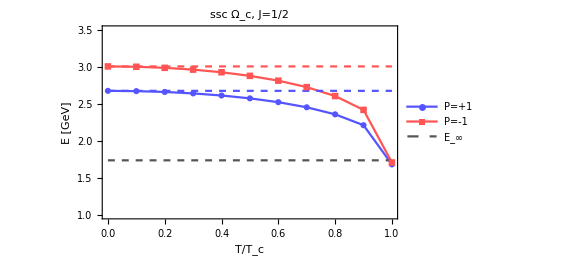

```mathematica
m1=sq;
m2=sq;
m3=cq;
fs=1;
gm=8;
excited=0;
pos=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,excited];
neg=temperatureData[1/2,-1,fs,gm,1,1/2,m1,m2,m3,excited];
imgSize=420;
imagePadding={{55,10},{50,10}};

SetOptions[ListPlot,
Frame->True,
Joined->True,
Axes->True,
ImagePadding->imagePadding,
FrameLabel->{"T/T_c","E [GeV]"},
PlotMarkers->{Automatic,Automatic,False,False,False},
ImageSize->imgSize,
LabelStyle->{FontFamily->"Arial",FontSize->14}];

E0=m1+m2+m3-1/2(3Cqqq)-(2.02*10^-3)/(m1*m2*m3);
dashedLine=Table[{t,E0},{t,0,1,0.1}];
dashedPos=Table[{t,pos[[1,2]]},{t,0,1,0.1}];
dashedNeg=Table[{t,neg[[1,2]]},{t,0,1,0.1}];

main=ListPlot[{pos,neg,dashedLine,dashedPos,dashedNeg},
PlotLabel->"ssc Ω_c, J=1/2",
PlotStyle->{Lighter[Blue],Lighter[Red],{Lighter[Black],Dashed},{Lighter[Blue],Dashed,Thin},{Lighter[Red],Dashed,Thin}},
PlotLegends->{"P=+1","P=-1","E_∞"},
PlotRange->{Automatic,{1,3.5}},
LabelStyle->{FontFamily->"Times",FontSize->14}
]
```

```mathematica
Export["plots/ch8_ssc_jhalf_pVSn.pdf",main,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch8_ssc_jhalf_pVSn.pdf

## Single baryon excited states as function of T/T_c

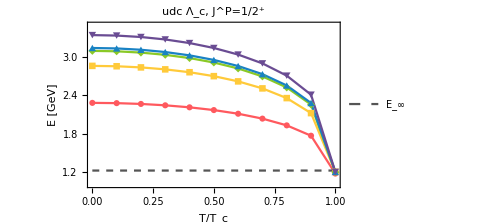

```mathematica
m1=uq;
m2=uq;
m3=cq;
fs=0;
gm=8;
pos1=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,0];
pos2=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,1];
pos3=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,2];
pos4=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,3];
pos5=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,4];
imgSize=360;
imagePadding={{50,10},{45,10}};

rgb[c1_,c2_,c3_]:=RGBColor[c1/255,c2/255,c3/255];

cScheme1={{rgb[234,172,139]},{rgb[229,107,111]},{rgb[181,101,118]},{rgb[109,89,122]},{rgb[53,80,112]},{Lighter[Black],Dashed,Thin}};
cScheme2={{rgb[246,170,28]},{rgb[188,57,8]},{rgb[148,27,12]},{rgb[98,23,8]},{rgb[34,9,1]},{Lighter[Black],Dashed,Thin}};
cScheme3={{rgb[255,89,94]},{rgb[255,202,58]},{rgb[138,201,38]},{rgb[25,130,196]},{rgb[106,76,147]},{Lighter[Black],Dashed,Thin}};

SetOptions[ListPlot,
Frame->True,
Joined->True,
Axes->True,
FrameLabel->{"T/T_c","E [GeV]"},
PlotMarkers->{Automatic,Automatic,Automatic,Automatic,Automatic,False},
ImagePadding->imagePadding,
ImageSize->imgSize,
PlotStyle->cScheme3,
LabelStyle->{FontFamily->"Arial",FontSize->14}];

E0=m1+m2+m3-1/2(3Cqqq);
dashedLine=Table[{t,E0},{t,0,1,0.1}];

main=ListPlot[{pos1,pos2,pos3,pos4,pos5,dashedLine},
PlotLabel->"udc Λ_c, J^P=1/2^+",
PlotRange->{Automatic,{1,3.5}},
PlotLegends->{None,None,None,None,None,"E_∞"}
]
```

```mathematica
Export["plots/ch8_udc_ladder.pdf",main,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch8_udc_ladder.pdf

## Expectation Values

```mathematica
hamiltonian=1
eigenvector=2
operatorMatrix=3
expectationValue=eigenvector.operator.eigenvector
```

1

2

3

2.3.2

```mathematica
?Hb
```